## Associations

Hello and welcome to our lecture on associations. Associations are a recent addition to Mathematica as they were added in version 10.

### Introduction

Associations are a special type of data structure that represent a mapping between a unique key and a value. In other languages, associations are typically known as dictionaries or hash maps. Let’s take a look at the definition:

```mathematica
?Association
```

RowBox[{"Association", "[", RowBox[{RowBox[{SubscriptBox[StyleBox["key", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["key", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "]"}] or RowBox[{"<|", RowBox[{RowBox[{SubscriptBox[StyleBox["key", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["key", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "|>"}] represents an association between keys and values.

So, we define an association with less than, pipe, and then pipe, less than. Let’s define a simple one:

```mathematica
letterToNumber = <|a->1,b->2,c->3|>
```

<|a→1,b→2,c→3|>

Let’s get the number for b:

```mathematica
letterToNumber[b]
```

2

The Keys function gets the keys from an association:

```mathematica
?Keys
```

Keys[<|key_1→val_1,key_2→val_2,…|>] gives a list of the keys key_i in an association.
Keys[{key_1→val_1,key_2→val_2,…}] gives a list of the key_i in a list of rules.

The keys of our association is:

```mathematica
Keys[letterToNumber]
```

{a,b,c}

The Values functions gets the values from an association:

```mathematica
?Values
```

Values[<|key_1→val_1,key_2→val_2,…|>] gives a list of the values val_i in an association.
Values[{key_1→val_1,key_2→val_2,…}] gives a list of the val_i in a list of rules.

The values of our association is:

```mathematica
Values[letterToNumber]
```

{1,2,3}

We can add a key value pair to the association using the Append function with a Rule:

```mathematica
letterToNumber=Append[letterToNumber,d->4]
```

<|a→1,b→2,c→3,d→4|>

If we add a key that already exists:

```mathematica
letterToNumber=Append[letterToNumber,a->Infinity]
```

<|b→2,c→3,d→4,a→∞|>

The value for the key is replaced. Now if we access a:

```mathematica
letterToNumber[a]
```

∞

It’s equal to infinity. We can also set the value of a key as follows:

```mathematica
letterToNumber[a]=1
```

1

```mathematica
letterToNumber
```

<|b→2,c→3,d→4,a→1|>

The function KeyExistsQ lets you check if a key exists:

```mathematica
KeyExistsQ[letterToNumber,a]
```

True

And if it doesn’t exist:

```mathematica
KeyExistsQ[leftHandWords,z]
```

False

It returns False.

### Database Example

Let’s do a little database example. Suppose you had the following data:

```mathematica
data={
<|"FirstName"->"Albert", "LastName"->"Einstein","FamousFor"->"Sciencing"|>,
<|"FirstName"->"Fred", "LastName"->"Astaire","FamousFor"->"Dancing"|>,
<|"FirstName"->"Lionel", "LastName"->"Messi","FamousFor"->"Footballing"|>,
<|"FirstName"->"Bill", "LastName"->"Gates","FamousFor"->"Computering"|>
}
```

{<|FirstName→Albert,LastName→Einstein,FamousFor→Sciencing|>,<|FirstName→Fred,LastName→Astaire,FamousFor→Dancing|>,<|FirstName→Lionel,LastName→Messi,FamousFor→Footballing|>,<|FirstName→Bill,LastName→Gates,FamousFor→Computering|>}

The function Lookup let’s us select specific fields from our data:

```mathematica
?Lookup
```

Lookup[assoc,key] looks up the value associated with key in the association assoc; if the key is not present, Missing[KeyAbsent,key] is returned.
Lookup[assoc,{key_1,key_2,…}] gives a list of the values associated with the key_i.
Lookup[{assoc_1,assoc_2,…},key] gives a list corresponding to the value of key in each assoc_i.
Lookup[assoc,key,default] gives default if the key is not present.
Lookup[key] represents an operator form of Lookup that can be applied to an expression.

Let’s get the LastName and FamousFor columns:

```mathematica
Lookup[data,{"LastName","FamousFor"}]
```

{{Einstein,Sciencing},{Astaire,Dancing},{Messi,Footballing},{Gates,Computering}}

To Select the association where FamousFor equals Computering:

```mathematica
Select[data,#["FamousFor"]=="Computering"&]
```

{<|FirstName→Bill,LastName→Gates,FamousFor→Computering|>}

We could also use a Case statement:

```mathematica
Cases[data,x_/;x["FamousFor"]=="Computering"]
```

{<|FirstName→Bill,LastName→Gates,FamousFor→Computering|>}

### Difference between Associations and Rule Replacements

Associations and Rule Replacements are actually very similar. The main difference is that a rule replacement can contain the same key more than once, whereas an association cannot:

```mathematica
rule={a->1,b->2,c->3,d->4,a->Infinity}
```

{a→1,b→2,c→3,d→4,a→∞}

You can use an association like a Rule Replacement:

```mathematica
b/.letterToNumber
```

2

In the same way you would use a Rule Replacement:

```mathematica
b/.rule
```

2

To replace an entry in a Rule Replacement:

```mathematica
rule/.(a->_)->(a->20)
```

{a→20,b→2,c→3,d→4,a→20}

There is one additional difference. Associations are implemented with a HashMap, which means that lookup of a key can be done in O(1), which essentially means that a lookup takes an amount of time that is independent of the number of keys in the HashMap.

Let’s demo this:

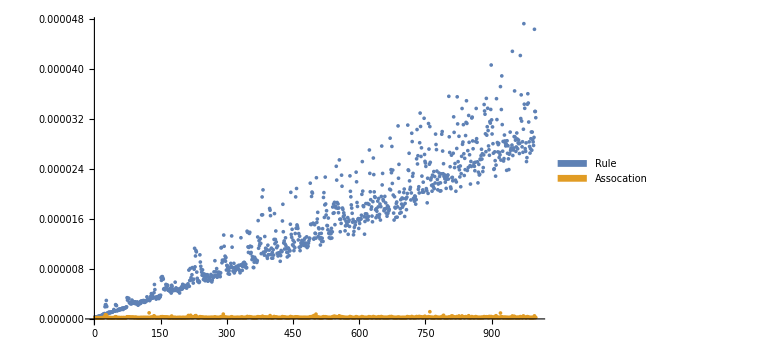
-Graphics-Size of Rule / AssociationTime in Seconds

```mathematica
Labeled[
ListPlot[
Transpose@
Table[
Module[{
samples=100,
numRule=Table[i->i,{i,1,j}],
numAssoc=Association[numRule],
randNumbers
},
randNumbers=RandomInteger[Length[numRule],samples];
{Timing[randNumbers/.numRule][[1]]/samples,Timing[randNumbers/.numAssoc][[1]]/samples}],
{j,1,1000,1}],
PlotLegends->SwatchLegend[{"Rule","Assocation"}],
Frame->Automatic,
ImageSize->Large],
{"Size of Rule / Association",Rotate["Time in Seconds",Pi/2]},{Bottom,Left}]
```

This code computes the timings for replacing 100 integers in a list using rule and association replacements whose sizes vary from 1 to 1000.

The x-axis represents the number of rules in the rule list, and the number of associations in the Association. The blue dots represent the timings for the rule replacement and the orange dots represent the timings for the association replacement.

As you can see, the time to perform a rule replacement increases as the size of the rule list increases, whereas the time to perform an association replacement remains constant as the size of the association increases. Pretty cool, huh?

In this lecture we learned about associations. Associations are super powerful and you can use them to make your code very efficient when you need to perform a lookup. We hope you had fun! See you at the next lecture.